```mathematica
Clear[a,μ, dr, eps,Q, kb, T]
μ=1*10^-2;
osseen[r_]:=1/(8 π μ)(IdentityMatrix[Length[r]]/Norm[r]+Outer[Times,r, r]/Norm[r]^3);
kernel[r_,a_]:=1/(((a/1.256)^2 π)^(3/2))Exp[(-r.r)/(a/1.256)^2];
nd[r_]:=(1/Norm[r])^3;

debye[r_]:=((eps kb T)/(2 nd[r] Q^2))^(1/2);

RPYl[r_,a_]:=1/(6 π μ a)(((3a)/(4 Norm[r])+a^3/(2 Norm[r]^3))IdentityMatrix[Length[r]]+((3a)/(4 Norm[r])-(3 a^3)/(2 Norm[r]^3))Outer[Times,r, r]/Norm[r]^2);
RPYs[r_,a_]:=1/(6 π μ a)((1-(9 Norm[r])/(32 a))IdentityMatrix[Length[r]]+((3 Norm[r])/(32 a))Outer[Times,r, r]/Norm[r]^2);
RPY[r_,a_]:=Which[Norm[r]≤2a,RPYs[r,a],Norm[r]> 2a,RPYl[r,a]];

dryTensor[r_,a_]:=1/(6 π μ a)IdentityMatrix[Length[r]];
coulomb[r_]:=Q^2/(4 π eps)r/Norm[r]^3;

coulombScreened[r_]:=Q^2/(4 π eps)(Exp[-Norm[r]/debye[r]](r+debye[r])r)/(Norm[r]^3 debye[r]);

p4[r_]:=Which[Abs[r]/dr≤1,(3-2 Abs[r]/dr+(1+4 Abs[r]/dr-4 r^2/dr^2)^(1/2))/8,
1<Abs[r]/dr≤2,(5-2 Abs[r]/dr-(-7+12 Abs[r]/dr-4 r^2/dr^2)^(1/2))/8,
 Abs[r]/dr ≥ 2,0];

p3[r_]:=Which[Abs[r]/dr≤0.5,(1+(1-3 r^2/dr^2)^(1/2))/3,
0.5<Abs[r]/dr≤1.5,(5-3 Abs[r]/dr-(-3(1- Abs[r]/dr)^2+1)^(1/2))/6,
 Abs[r]/dr ≥ 1.5,0];

peskin4[r_]:=p4[r[[1]]]p4[r[[2]]]p4[r[[3]]]/dr^3;
peskin3[r_]:=p3[r[[1]]]p3[r[[2]]]p3[r[[3]]]/dr^3;
```

2

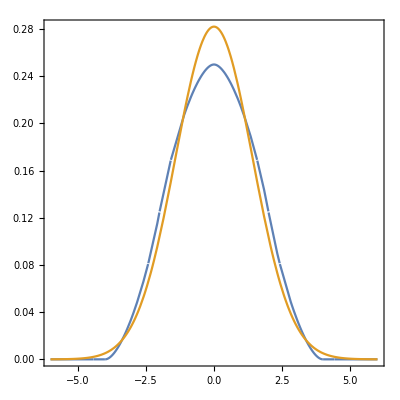

```mathematica
dr=2
Plot[{p4[r]/dr,1/(dr π^(1/2))Exp[-r^2/dr^2]},{r,-3 dr,3dr},Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
Integrate[1/(dr π^(1/2))Exp[-r^2/dr^2],{r,-∞,∞}]
Integrate[p4[r]/dr,{r,-∞,∞}]
```

1

1

```mathematica
T=295;
kb=1.38065*10^-16;
diff=0.5(1.17+1.33)*10^-5;
diffA=(1.17)*10^-5;
diffB=(1.33)*10^-5;
μ=0.01;
Q=1.6*10^-19;
eps = 692.96*10^-21;
aReal=(kb T)/(diff μ 6 π)
aA=(kb T)/(diffA μ 6 π)
aB=(kb T)/(diffB μ 6 π)

(aA+aB)/2
```

1.7286×10^-8

1.84679×10^-8

1.62462×10^-8

1.73571×10^-8

```mathematica
n=4*5*2*6.02*10^19
radsA=(1/n^(1/3))/aReal
radsB=0.55*(1/n^(1/3))/aReal
radsR=4.326863*10^-8/aReal
```

2.408×10^21

4.31605

2.37383

2.5031

```mathematica
velRPY[r_,a_,sep_]:= RPY[r,a].(coulomb[sep]);
velDry[r_,a_,sep_]:= dryTensor[r,a].coulomb[sep];

velRPYscreened[r_,a_,sep_]:= RPY[r,a].(coulombScreened[sep]);
velDryscreened[r_,a_,sep_]:= dryTensor[r,a].coulombScreened[sep];
```

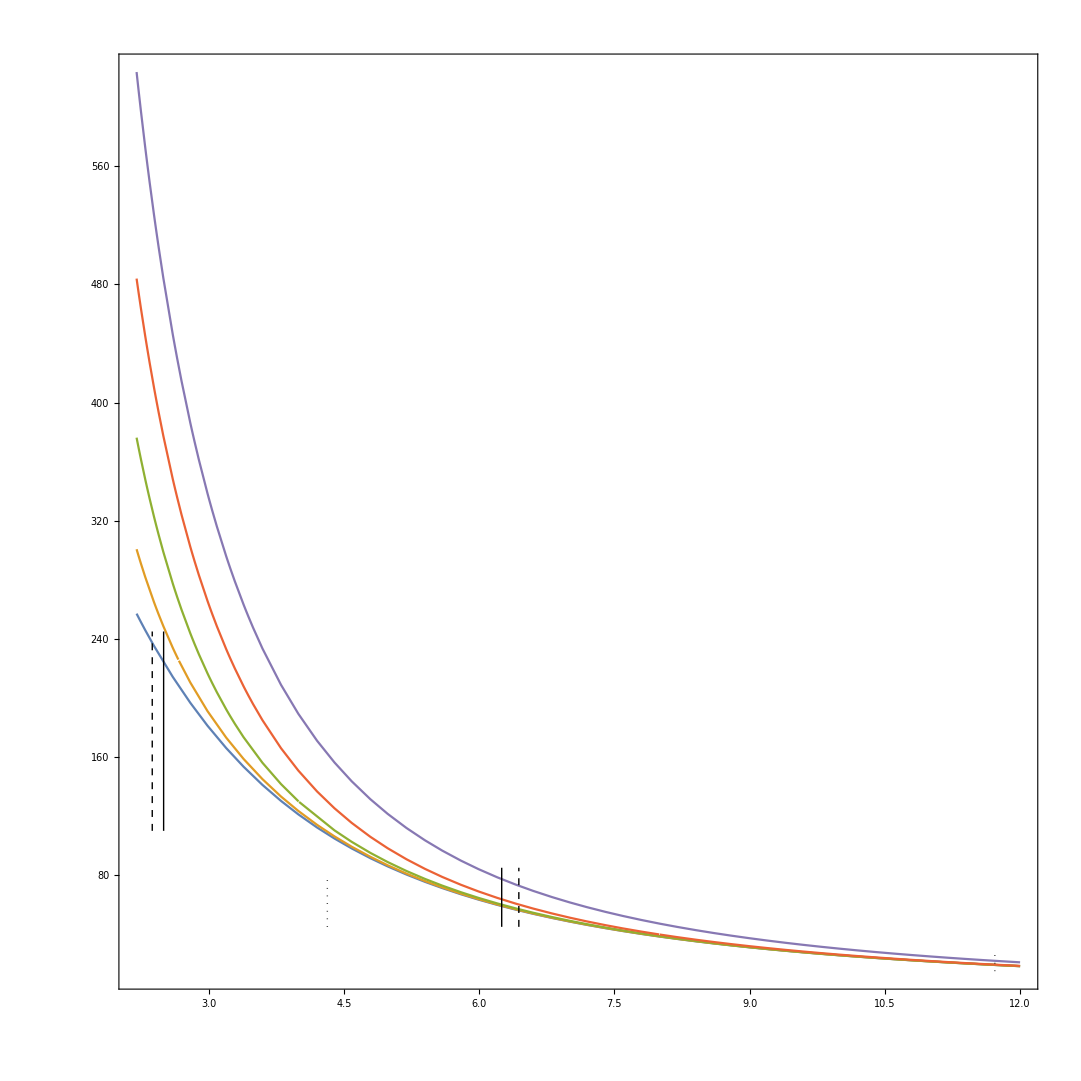

```mathematica
pa=Plot[{
velRPY[aReal{r,0,0},aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},1.3333aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},2aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},4aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]]}
,{r,2.2,12},PlotRange->All];
pb1=Graphics[{Line[{{6.25,45},{6.25,85}}],Dashed,Line[{{6.44,45},{6.44,85}}],Dotted,Line[{{11.72,15},{11.72,28}}]}];
pb2=Graphics[{Line[{{3.70,110},{3.70,245}}],Dashed,Line[{{3.77,110},{3.77,245}}],Dotted,Line[{{6.85,45},{6.85,80}}]}];
pb3=Graphics[{Line[{{2.5,110},{2.5,245}}],Dashed,Line[{{2.3738,110},{2.3738,245}}],Dotted,Line[{{4.3160,45},{4.3160,80}}]}];
Show[pa,pb1,pb3,Frame->True,AspectRatio->1,Axes->False]
```

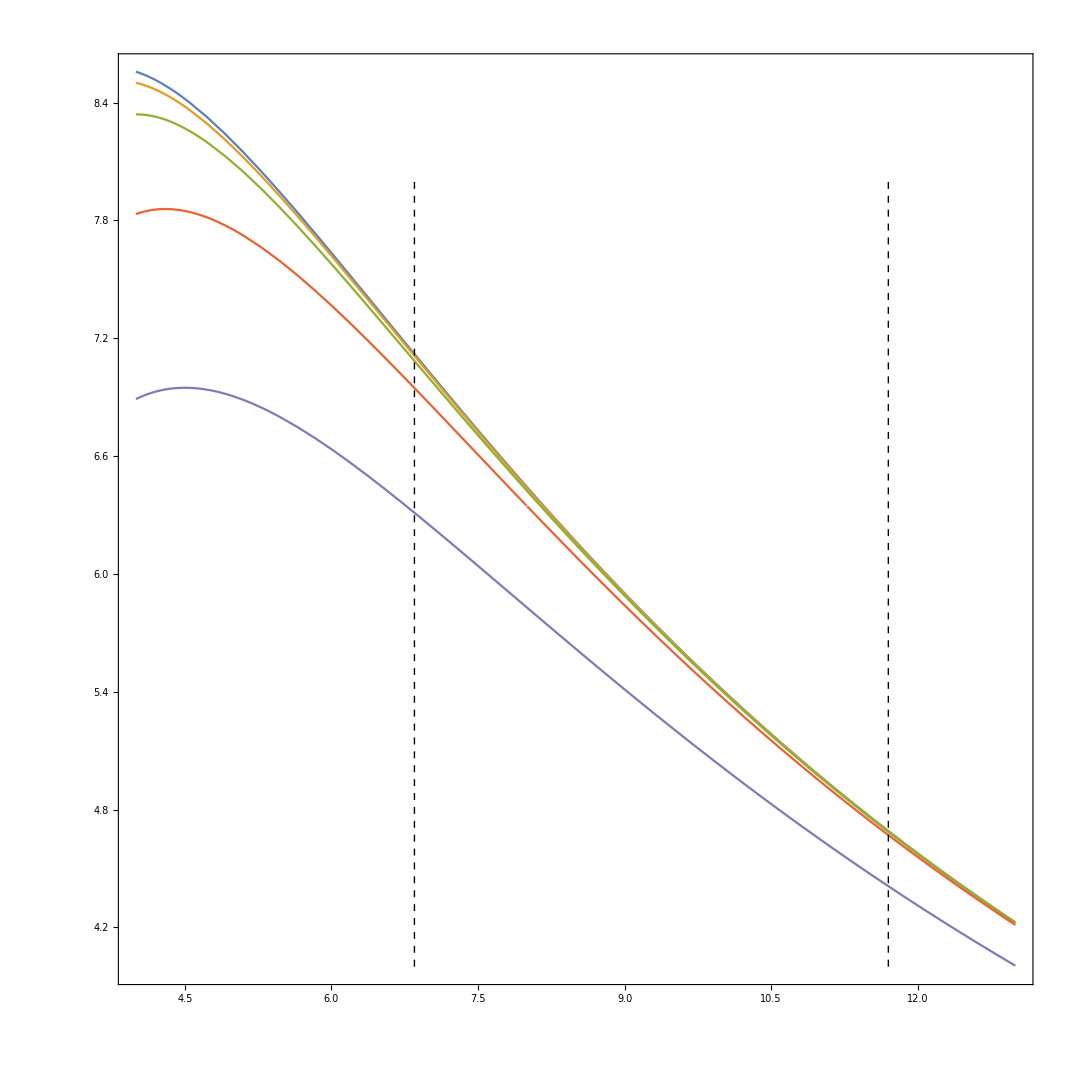

6.41282

7.28979

6.85131

6.85131

```mathematica
pa=Plot[{
velRPYscreened[aReal{r,0,0},aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},1.3333aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},2aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},4aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]]}
,{r,4,13},PlotRange->All];
pb=Graphics[{Dashed,Line[{{6.85,4},{6.85,8}}],Line[{{11.7,4},{11.7,8}}]}];
Show[pa,pb,Frame->True,AspectRatio->1,Axes->False]
```

2.02515×10^-7

1.11383×10^-7

1.08×10^-7

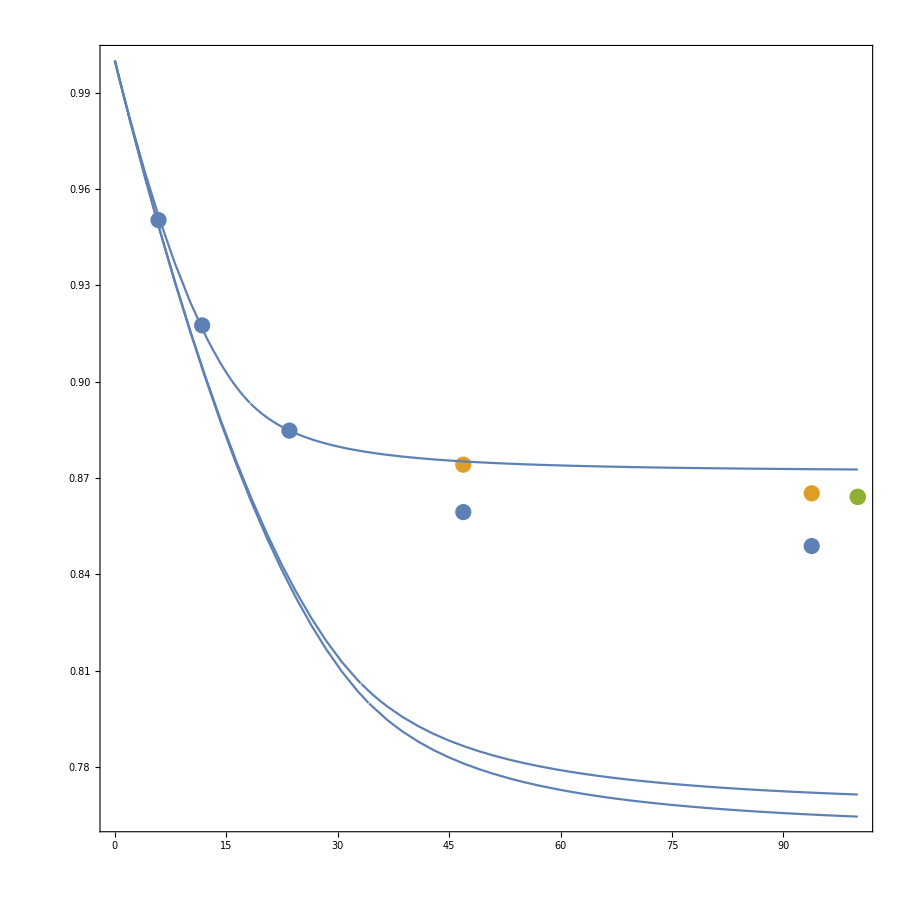

0.848837

6.85131

```mathematica
n=2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=1.08*10^-7

rads=0.55radsM;
pointsZero={{93.8,8.03/9.46},{46.9,8.13/9.46},{23.5,8.37/9.46},{11.75,8.68/9.46},{5.88,8.99/9.46}};
pointsWeak={{93.8,7.77/8.98},{46.9,7.85/8.98}};
pointsTheory={{100,7.76/8.98}};
pointsStrong={{93.8,8.37/9.43},{46.9,8.41/9.43}};
pc=ListPlot[{pointsZero,pointsWeak,pointsTheory}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,PlotRange->All,Frame->True,AspectRatio->1,Axes->False]
```

1.18432×10^-7

6.51374×10^-8

6.39×10^-8

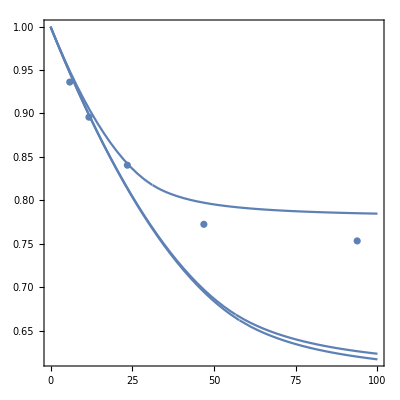

```mathematica
n=5*2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=6.39*10^-8

pointsZero={{5.88,4.4/4.7},{11.75,4.21/4.70},{23.5,3.95/4.70},{46.9,3.63/4.70},{93.8,3.54/4.70}};
pc=ListPlot[{pointsZero}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(per/100 diffA 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[aReal{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,Frame->True,PlotRange->All,AspectRatio->1,Axes->False]
```

7.46073×10^-8

4.1034×10^-8

4.32686×10^-8

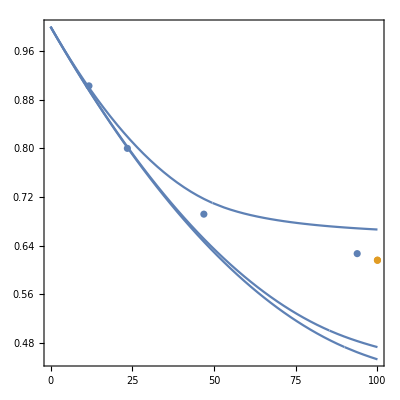

```mathematica
n=20*2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=4.326863*10^-8

pointsZero={{11.75,1.67/1.85},{23.5,1.48/1.85},{46.9,1.28/1.85},{93.8,1.16/1.85}};
pointsTheory={{100,1.14/1.85}};
pc=ListPlot[{pointsZero,pointsTheory}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(per/100 diffA 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[aReal{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,Frame->True,PlotRange->All,AspectRatio->1,Axes->False]
```

```mathematica
Q/(kb T)10^14 0.96*10^-7
```

37.7125

```mathematica
Q 10^14
```

0.000016

```mathematica
velRPY[aReal{10,0,0},aReal,-aReal{10,0,0}][[1]]
velRPY[aReal{0.000001,0,0},aReal,aReal{10,0,0}][[1]]
velField[aReal{0.000001,0,0},aReal,aReal{10,0,0}][[1]]
```

-3.68936

24.7608

4596.21

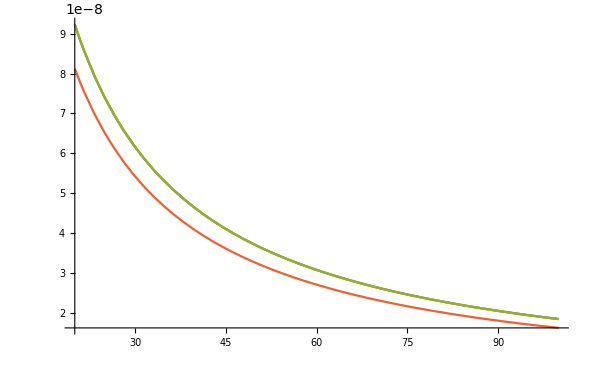

```mathematica
Plot[{(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),0.5((kb T)/((per/100 diffA) 6 μ π)+(kb T)/((0.881 per/100 diffB) 6 μ π)),((kb T)/((per/100 diffA) 6 μ π)),((kb T)/((per/100 diffB) 6 μ π))},{per,20,100}]
```

```mathematica
n=5*6.02*10^19;
(1/n^(1/3))
0.55(1/n^(1/3))
```

1.49215×10^-7

8.2068×10^-8

```mathematica
dataA=Import["/home/drladiges/kumonga/projects/FHDeX/exec/NN_test4/nearestNeighbour","Table"];
```

```mathematica
Mean[dataA[[-3;;-1]]]
```

{5.89375×10^-8,4.57637×10^-8,4.57889×10^-8,5.92056×10^-8,4.32686×10^-8}

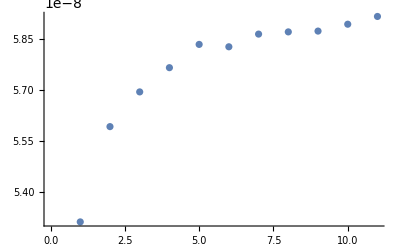

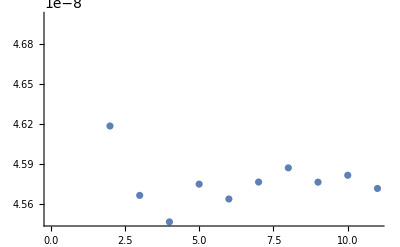

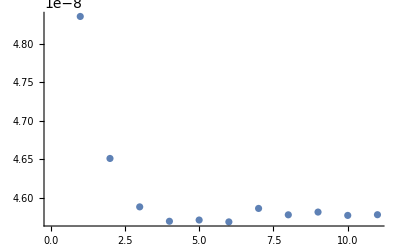

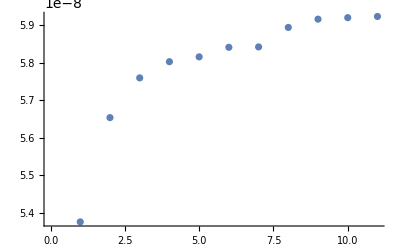

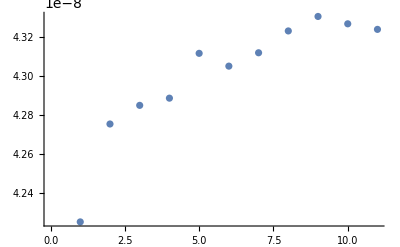

```mathematica
ListPlot[dataA[[All,1]]]
ListPlot[dataA[[All,2]]]
ListPlot[dataA[[All,3]]]
ListPlot[dataA[[All,4]]]
ListPlot[dataA[[All,5]]]
```

```mathematica
n=20*2*6.02*10^19;
radsA=(1/n^(1/3))/aReal
radsB=0.55*(1/n^(1/3))/aReal
```

4.31605

2.37383

{{{93.8,1/100},ErrorBar[3/500]},{{46.9,1/500},ErrorBar[7/1000]},{{23.5,1/50},ErrorBar[7/1000]},{{11.75,13/1000},ErrorBar[1/500]},{{5.88,19/500},ErrorBar[1/125]},{{0,43/500},ErrorBar[3/500]}}

{{{93.8,0.0347938},ErrorBar[0.00515464]},{{46.9,0.0476804},ErrorBar[0.00386598]},{{23.5,0.0786082},ErrorBar[0.00902062]},{{11.75,0.118557},ErrorBar[0.0115979]},{{5.88,0.158505},ErrorBar[0.0115979]},{{0,0.219072},ErrorBar[0.00515464]}}

{{{93.8,0.00128866},ErrorBar[0.00257732]},{{46.9,0.0115979},ErrorBar[0.00386598]},{{23.5,0.0115979},ErrorBar[0.00257732]},{{11.75,0.0708763},ErrorBar[0.00257732]},{{5.88,0.122423},ErrorBar[0.00257732]},{{0,0.157216},ErrorBar[0.00257732]}}

{{{93.8,-0.0152941},ErrorBar[0.00235294]},{{46.9,-0.0105882},ErrorBar[0.00352941]},{{23.5,0.00117647},ErrorBar[0.00235294]},{{11.75,0.0235294},ErrorBar[0.00235294]},{{5.88,0.0517647},ErrorBar[0.00235294]},{{0,0.109412},ErrorBar[0.00235294]}}

{{{0,0.407186},ErrorBar[0.00598802]},{{5.88,0.317365},ErrorBar[0.0598802]},{{11.75,0.260479},ErrorBar[0.00898204]},{{23.5,0.182635},ErrorBar[0.00598802]},{{46.9,0.0868263},ErrorBar[0.00598802]},{{93.8,0.0598802},ErrorBar[0.0149701]}}

{{{0,0.622807},ErrorBar[0.0175439]},{{5.88,0.491228},ErrorBar[0.0877193]},{{11.75,0.464912},ErrorBar[0.0263158]},{{23.5,0.298246},ErrorBar[0.0263158]},{{46.9,0.122807},ErrorBar[0.0175439]},{{93.8,0.0175439},ErrorBar[0.0263158]}}

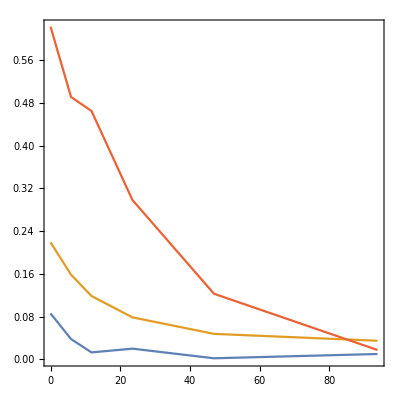

```mathematica
Needs["ErrorBarPlots`"];
points001err={{93.8,(1010-1000)/1000-(1010+0006-1000)/1000},
{46.9,(1002-1000)/1000-(1002+0007-1000)/1000},
{23.5,(1020-1000)/1000-(1020+0007-1000)/1000},
{11.75,(1013-1000)/1000-(1013+0002-1000)/1000},
{5.88,(1038-1000)/1000-(1038+0008-1000)/1000},
{0,(1086-1000)/1000-(1086+0006-1000)/1000}};
points001={{93.8,(1010-1000)/1000},
{46.9,(1002-1000)/1000},
{23.5,(1020-1000)/1000},
{11.75,(1013-1000)/1000},
{5.88,(1038-1000)/1000},
{0,(1086-1000)/1000}};
points001Plot=Table[{points001[[ii]],ErrorBar[-points001err[[ii,2]]]},{ii,1,Length[points001]}]
points01={{93.8,(8.03-7.76)/7.76},{46.9,(8.13-7.76)/7.76},{23.5,(8.37-7.76)/7.76},{11.75,(8.68-7.76)/7.76},{5.88,(8.99-7.76)/7.76},{0,(9.46-7.76)/7.76}};
points01err={{93.8,(8.03-7.76)/7.76-(8.03+0.04-7.76)/7.76},
{46.9,(8.13-7.76)/7.76-(8.13+0.03-7.76)/7.76},
{23.5,(8.37-7.76)/7.76-(8.37+0.07-7.76)/7.76},
{11.75,(8.68-7.76)/7.76-(8.68+0.09-7.76)/7.76},
{5.88,(8.99-7.76)/7.76-(8.99+0.09-7.76)/7.76},
{0,(9.46-7.76)/7.76-(9.46+0.04-7.76)/7.76}};
points01Plot=Table[{points01[[ii]],ErrorBar[-points01err[[ii,2]]]},{ii,1,Length[points01]}]

points01w={{93.8,(7.77-7.76)/7.76},{46.9,(7.85-7.76)/7.76},{23.5,(7.85-7.76)/7.76},{11.75,(8.31-7.76)/7.76},{5.88,(8.71-7.76)/7.76},{0,(8.98-7.76)/7.76}};
points01werr={{93.8,(7.77-7.76)/7.76-(7.77+0.02-7.76)/7.76},
{46.9,(7.85-7.76)/7.76-(7.85+0.03-7.76)/7.76},
{23.5,(7.85-7.76)/7.76-(7.85+0.02-7.76)/7.76},
{11.75,(8.31-7.76)/7.76-(8.31+0.02-7.76)/7.76},
{5.88,(8.71-7.76)/7.76-(8.71+0.02-7.76)/7.76},
{0,(8.98-7.76)/7.76-(8.98+0.02-7.76)/7.76}};
points01wPlot=Table[{points01w[[ii]],ErrorBar[-points01werr[[ii,2]]]},{ii,1,Length[points01w]}]

points01s={{93.8,(8.37-8.50)/8.50},{46.9,(8.41-8.50)/8.50},{23.5,(8.51-8.50)/8.50},{11.75,(8.70-8.50)/8.50},{5.88,(8.94-8.50)/8.50},{0,(9.43-8.50)/8.50}};
points01serr={{93.8,(8.37-8.50)/8.50-(8.37+0.02-8.50)/8.50},
{46.9,(8.41-8.50)/8.50-(8.41+0.03-8.50)/8.50},
{23.5,(8.51-8.50)/8.50-(8.51+0.02-8.50)/8.50},
{11.75,(8.51-8.50)/8.50-(8.51+0.02-8.50)/8.50},
{5.88,(8.70-8.50)/8.50-(8.70+0.02-8.50)/8.50},
{0,(8.94-8.50)/8.50-(8.94+0.02-8.50)/8.50}};
points01sPlot=Table[{points01s[[ii]],ErrorBar[-points01serr[[ii,2]]]},{ii,1,Length[points01s]}]


points05={{0,(4.7-3.34)/3.34},
{5.88,(4.4-3.34)/3.34},
{11.75,(4.21-3.34)/3.34},
{23.5,(3.95-3.34)/3.34},
{46.9,(3.63-3.34)/3.34},
{93.8,(3.54-3.34)/3.34}};
points05err={{0,(4.7-3.34)/3.34-(4.7+0.02-3.34)/3.34},{5.88,(4.4-3.34)/3.34-(4.4+0.2-3.34)/3.34},
{11.75,(4.21-3.34)/3.34-(4.21+0.03-3.34)/3.34},
{23.5,(3.95-3.34)/3.34-(3.95+0.02-3.34)/3.34},
{46.9,(3.63-3.34)/3.34-(3.63+0.02-3.34)/3.34},
{93.8,(3.54-3.34)/3.34-(3.54+0.05-3.34)/3.34}};
points05Plot=Table[{points05[[ii]],ErrorBar[-points05err[[ii,2]]]},{ii,1,Length[points05]}]

points20={{0,(1.85-1.14)/1.14},{5.88,(1.7-1.14)/1.14},{11.75,(1.67-1.14)/1.14},{23.5,(1.48-1.14)/1.14},{46.9,(1.28-1.14)/1.14},{93.8,(1.16-1.14)/1.14}};
points20err={{0,(1.85-1.14)/1.14-(1.85+0.02-1.14)/1.14},
{5.88,(1.7-1.14)/1.14-(1.7+0.1-1.14)/1.14},
{11.75,(1.67-1.14)/1.14-(1.67+0.03-1.14)/1.14},
{23.5,(1.48-1.14)/1.14-(1.48+0.03-1.14)/1.14},
{46.9,(1.28-1.14)/1.14-(1.28+0.02-1.14)/1.14},
{93.8,(1.16-1.14)/1.14}-(1.16+0.03-1.14)/1.14};
points20Plot=Table[{points20[[ii]],ErrorBar[-points20err[[ii,2]]]},{ii,1,Length[points20]}]
ListPlot[{points001,points01,points05Plot,points20},Joined->True,PlotRange->All,Axes->False,Frame->True,AspectRatio->1]
```

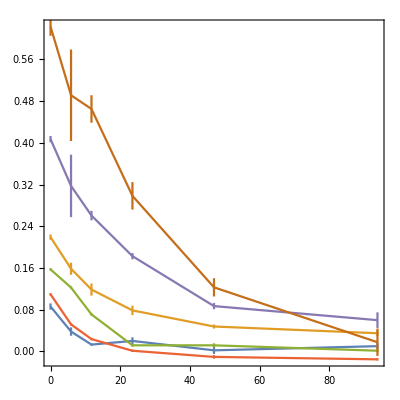

```mathematica
ErrorListPlot[{points001Plot,points01Plot,points01wPlot,points01sPlot,points05Plot,points20Plot},Joined->True,PlotRange->All,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
dims={13.06*10^-7,13.06*10^-7,6.53*10^-7};
domainParts=87;
wallPartsX = 40;
wallPartsZ = 20;
wallTotal = wallPartsX*wallPartsZ; 

xCell=dims[[1]]/wallPartsX;
zCell =dims[[3]]/wallPartsZ;

wallPosBottom = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTop = Flatten[Table[{xCell/2+xCell*ii,0.75dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPos=Join[wallPosBottom,wallPosTop];

images=0;

wallPosPeriodic=Flatten[Table[Join[Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.25*dims[[2]]+qq*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1],Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.75*dims[[2]]+qq*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1]],{oo,-images,images},{pp,-images,images},{qq,-images,images}],2];
```

```mathematica
dims={16*104.48*10^-7,52.24*10^-7,52.24*10^-7};
count =(2*4096)/8
sep=dims[[1]]/count
images=0;
wallPos=Table[{sep/2+ii*sep,0.5dims[[2]],0.5dims[[3]]},{ii,0,count-1}];
(*wallPos={{0.5dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.375dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.625dims[[1]],0.5dims[[2]],0.5dims[[3]]}};*)
wallPosPeriodic=Table[{wallPos[[ii,1]],wallPos[[ii,2]],wallPos[[ii,3]]+qq*dims[[2]]},{qq,-images,images},{ii,1,Length[wallPos]}];
Length[wallPosPeriodic]
```

1024

1.6325×10^-7

1

```mathematica
dims={3.265*10^-7,52.24*10^-7,52.24*10^-7};
count =16/8
sep=dims[[1]]/count

wallPos=Table[{sep/2+ii*sep,0.5dims[[2]],0.5dims[[3]]},{ii,0,count-1}]
(*wallPos={{0.5dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.375dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.625dims[[1]],0.5dims[[2]],0.5dims[[3]]}};*)
wallPosPeriodic={wallPos};
```

2

1.6325×10^-7

{{8.1625×10^-8,2.612×10^-6,2.612×10^-6},{2.44875×10^-7,2.612×10^-6,2.612×10^-6}}

```mathematica
aa=2.561*10^-8;
μ=0.9*10^-2;
mob=Sum[ArrayFlatten[Table[Table[If[wallPos[[jj]]-wallPosPeriodic[[pp,ii]]=={0,0,0},dryTensor[{0,0,0},aa],RPY[wallPos[[jj]]-wallPosPeriodic[[pp,ii]],aa]],{ii,1,Length[wallPos]}],{jj,1,Length[wallPos]}]],{pp,1,Length[wallPosPeriodic]}];
(*mobGL=ArrayFlatten[Table[Table[RPY[wallPosBottom[[jj]]-wallPosBottomGL[[ii]],aa],{ii,1,Length[wallPosBottomGL]}],{jj,1,Length[wallPosBottom]}]];*)
```

```mathematica
Length[mob[[1]]]
Length[force]
count
```

192

192

64

```mathematica
mobInv=Inverse[matC];
```

```mathematica
q=1.6*10^-19;
f=10*10^12;
force=Flatten[Table[{q*f,0,0},{ii,1,count}]];
```

```mathematica
vel=mob.force;
vel[[2*256*3-2]]
vel[[2*256*3-2]]
```

1546.11

1546.11

```mathematica
matC//MatrixForm
```

(4.79164×10^8 | 0.114208 | 0.0153085 | 4.15772×10^7 | 0.142424 | 0.0153952 | 6.19848×10^7 | 0.135043 | 0.0144684 | 4.7339×10^7 | 0.14009 | 0.0154748 | 2.09863×10^7 | 0.980536 | 0.025708 | 2.09015×10^7 | 0.980283 | 0.0252754 | 2.12759×10^7 | 0.978887 | 0.0261627 | 2.11601×10^7 | 0.9759 | 0.0252828
-0.00170283 | 4.27993×10^8 | -0.0230235 | -0.00478696 | -7.5034×10^6 | 0.00454119 | -3.76218×10^-9 | -7.5034×10^6 | 0.00332634 | 0.00900759 | -9.60103×10^6 | -0.00248743 | -0.0044626 | 378983. | -0.00156645 | 0.000582076 | -25303.2 | -0.00242279 | -2.71232×10^-9 | -25303.2 | -0.000563917 | -0.00476 | -325752. | -0.00198862
0.000117547 | -0.0153085 | 4.79164×10^8 | 805.272 | -0.0144637 | 6.19855×10^7 | 775.697 | -0.0153906 | 4.1578×10^7 | 805.271 | -0.01547 | 4.73398×10^7 | 767.496 | -0.0593418 | 2.09871×10^7 | 1039.1 | -0.055677 | 2.12768×10^7 | 915.422 | -0.055772 | 2.09025×10^7 | 1039.09 | -0.0555335 | 2.11611×10^7
4.1578×10^7 | 0.142411 | 0.015378 | 4.79163×10^8 | 0.114208 | 0.0153256 | 4.7339×10^7 | 0.140107 | 0.0154945 | 6.19847×10^7 | 0.135029 | 0.0144533 | 2.09017×10^7 | 0.980778 | 0.025311 | 2.0986×10^7 | 0.980066 | 0.0256712 | 2.11602×10^7 | 0.97544 | 0.0252476 | 2.12758×10^7 | 0.979367 | 0.0261983
0.00242971 | -7.5034×10^6 | 0.00453816 | 0.000728337 | 4.27993×10^8 | -0.0230336 | 0.00237332 | -9.60103×10^6 | -0.00248737 | -0.004949 | -7.5034×10^6 | 0.00332437 | 0.00613623 | -25303.2 | -0.00242356 | 0.00341747 | 378983. | -0.00156767 | 0.000195114 | -325752. | -0.00198763 | 0.000760438 | -25303.2 | -0.00056585
0.00018402 | -0.0144533 | 6.19855×10^7 | 805.274 | -0.0153209 | 4.79164×10^8 | 775.671 | -0.01549 | 4.73398×10^7 | 805.283 | -0.0153732 | 4.1578×10^7 | 767.484 | -0.0557237 | 2.12768×10^7 | 1039.1 | -0.0592725 | 2.09871×10^7 | 915.423 | -0.0554792 | 2.11611×10^7 | 1039.09 | -0.0558045 | 2.09025×10^7
6.19855×10^7 | 0.135034 | 0.0144533 | 4.7339×10^7 | 0.140107 | 0.0154945 | 4.79163×10^8 | 0.114208 | 0.0153256 | 4.15772×10^7 | 0.142406 | 0.015378 | 2.1276×10^7 | 0.979374 | 0.0261983 | 2.11601×10^7 | 0.975437 | 0.0252476 | 2.09861×10^7 | 0.980069 | 0.0256712 | 2.09015×10^7 | 0.98077 | 0.025311
0.00145741 | -7.5034×10^6 | 0.00332438 | 0.00899746 | -9.60103×10^6 | -0.00248738 | -0.00237332 | 4.27993×10^8 | -0.0230336 | -0.00477683 | -7.5034×10^6 | 0.00453816 | 0.0000764291 | -25303.2 | -0.000565849 | -0.00475906 | -325752. | -0.00198763 | -0.00019512 | 378983. | -0.00156767 | 0.000581135 | -25303.2 | -0.00242356
-0.000422861 | -0.015378 | 4.1578×10^7 | 805.271 | -0.0154898 | 4.73398×10^7 | 775.694 | -0.0153211 | 4.79164×10^8 | 805.272 | -0.0144486 | 6.19855×10^7 | 767.489 | -0.0558119 | 2.09025×10^7 | 1039.09 | -0.0554759 | 2.11611×10^7 | 915.425 | -0.0592758 | 2.09871×10^7 | 1039.1 | -0.0557163 | 2.12768×10^7
4.73398×10^7 | 0.140094 | 0.0154748 | 6.19847×10^7 | 0.135043 | 0.0144684 | 4.15772×10^7 | 0.142424 | 0.0153952 | 4.79163×10^8 | 0.114204 | 0.0153085 | 2.11604×10^7 | 0.975907 | 0.0252828 | 2.12758×10^7 | 0.978883 | 0.0261627 | 2.09016×10^7 | 0.980287 | 0.0252754 | 2.0986×10^7 | 0.980529 | 0.025708
-0.00237178 | -9.60103×10^6 | -0.00248744 | -0.00495913 | -7.5034×10^6 | 0.00332635 | -9.83839×10^-9 | -7.5034×10^6 | 0.00454119 | 0.000738462 | 4.27993×10^8 | -0.0230235 | -0.00148859 | -325752. | -0.00198862 | 0.000761379 | -25303.2 | -0.000563916 | -4.13261×10^-9 | -25303.2 | -0.00242279 | 0.00341653 | 378983. | -0.00156645
0.000244527 | -0.0154748 | 4.73398×10^7 | 805.283 | -0.0153905 | 4.1578×10^7 | 775.682 | -0.0144638 | 6.19855×10^7 | 805.274 | -0.0153038 | 4.79164×10^8 | 767.494 | -0.0555409 | 2.11611×10^7 | 1039.09 | -0.0557686 | 2.09025×10^7 | 915.426 | -0.0556803 | 2.12768×10^7 | 1039.1 | -0.0593344 | 2.09871×10^7
2.0987×10^7 | 0.261335 | -0.0153137 | 2.09017×10^7 | 0.261434 | -0.0159597 | 2.1276×10^7 | 0.261695 | -0.0151815 | 2.11603×10^7 | 0.261966 | -0.0161378 | 4.79163×10^8 | 0.902738 | -0.0244892 | 4.15769×10^7 | 0.851558 | -0.0253274 | 6.19846×10^7 | 0.827656 | -0.0249826 | 4.73387×10^7 | 0.846964 | -0.0255381
0.000363214 | 378983. | -0.00217468 | 0.000664019 | -25303.2 | -0.00279528 | -4.28279×10^-9 | -25303.2 | -0.00174331 | -0.00279568 | -325752. | -0.00337055 | 0.00250132 | 4.27993×10^8 | -0.00673573 | -0.00587913 | -7.5034×10^6 | 0.00480489 | -3.33704×10^-9 | -7.5034×10^6 | 0.00305335 | 0.000614464 | -9.60103×10^6 | -0.00401223
-0.000428437 | 0.0153137 | 2.09871×10^7 | 804.443 | 0.0151862 | 2.12768×10^7 | 774.491 | 0.0159643 | 2.09025×10^7 | 804.438 | 0.0161426 | 2.11611×10^7 | 766.616 | 0.0299605 | 4.79164×10^8 | 1039.88 | 0.0247827 | 6.19855×10^7 | 916.728 | 0.0260883 | 4.1578×10^7 | 1039.85 | 0.0238663 | 4.73398×10^7
2.09025×10^7 | 0.261299 | -0.0159436 | 2.09863×10^7 | 0.261473 | -0.0153302 | 2.11603×10^7 | 0.262107 | -0.0161552 | 2.1276×10^7 | 0.261554 | -0.0151659 | 4.15772×10^7 | 0.851929 | -0.0253654 | 4.79163×10^8 | 0.902297 | -0.024451 | 4.73388×10^7 | 0.846606 | -0.025502 | 6.19845×10^7 | 0.827996 | -0.0250199
0.0000711518 | -25303.2 | -0.00278851 | 0.00138906 | 378983. | -0.00217152 | -0.00050777 | -325752. | -0.00336602 | 0.000742573 | -25303.2 | -0.00173858 | -0.00576168 | -7.5034×10^6 | 0.00480884 | 0.010597 | 4.27993×10^8 | -0.00676741 | -0.00697491 | -9.60103×10^6 | -0.00400835 | -0.00533232 | -7.5034×10^6 | 0.00305139
-0.000248254 | 0.0151659 | 2.12768×10^7 | 804.443 | 0.015335 | 2.09871×10^7 | 774.492 | 0.0161597 | 2.11611×10^7 | 804.437 | 0.0159483 | 2.09025×10^7 | 766.618 | 0.0248096 | 6.19855×10^7 | 1039.86 | 0.0299289 | 4.79164×10^8 | 916.707 | 0.0238283 | 4.73398×10^7 | 1039.86 | 0.0261216 | 4.1578×10^7
2.12768×10^7 | 0.261559 | -0.0151659 | 2.11603×10^7 | 0.262107 | -0.0161552 | 2.09863×10^7 | 0.261473 | -0.0153302 | 2.09017×10^7 | 0.261294 | -0.0159436 | 6.19848×10^7 | 0.828003 | -0.0250199 | 4.73387×10^7 | 0.846602 | -0.025502 | 4.79163×10^8 | 0.9023 | -0.024451 | 4.15769×10^7 | 0.851921 | -0.0253654
-0.000383618 | -25303.2 | -0.00173858 | -0.00280608 | -325752. | -0.00336602 | 0.00050776 | 378983. | -0.00217152 | 0.000674421 | -25303.2 | -0.00278851 | -0.000979286 | -7.5034×10^6 | 0.00305139 | 0.000615457 | -9.60103×10^6 | -0.00400836 | 0.0069749 | 4.27993×10^8 | -0.00676742 | -0.00588012 | -7.5034×10^6 | 0.00480883
0.000402425 | 0.0159436 | 2.09025×10^7 | 804.438 | 0.0161599 | 2.11611×10^7 | 774.497 | 0.0153348 | 2.09871×10^7 | 804.443 | 0.0151706 | 2.12768×10^7 | 766.625 | 0.0261142 | 4.1578×10^7 | 1039.85 | 0.0238317 | 4.73398×10^7 | 916.732 | 0.0299255 | 4.79164×10^8 | 1039.88 | 0.0248169 | 6.19855×10^7
2.11611×10^7 | 0.261971 | -0.0161378 | 2.1276×10^7 | 0.261695 | -0.0151815 | 2.09017×10^7 | 0.261434 | -0.0159597 | 2.09863×10^7 | 0.261331 | -0.0153137 | 4.7339×10^7 | 0.846972 | -0.0255381 | 6.19845×10^7 | 0.827653 | -0.0249826 | 4.15771×10^7 | 0.851561 | -0.0253274 | 4.79163×10^8 | 0.902731 | -0.0244892
-0.000083991 | -325752. | -0.00337055 | 0.000732173 | -25303.2 | -0.00174331 | -9.62345×10^-9 | -25303.2 | -0.00279528 | 0.00139946 | 378983. | -0.00217468 | 0.00417302 | -9.60103×10^6 | -0.00401223 | -0.00533134 | -7.5034×10^6 | 0.00305336 | -5.22505×10^-9 | -7.5034×10^6 | 0.0048049 | 0.010596 | 4.27993×10^8 | -0.00673571
0.000223712 | 0.0161378 | 2.11611×10^7 | 804.437 | 0.0159644 | 2.09025×10^7 | 774.498 | 0.0151861 | 2.12768×10^7 | 804.443 | 0.0153184 | 2.09871×10^7 | 766.624 | 0.023859 | 4.73398×10^7 | 1039.86 | 0.0260917 | 4.1578×10^7 | 916.725 | 0.0247794 | 6.19855×10^7 | 1039.86 | 0.0299679 | 4.79164×10^8)

```mathematica
mobInv//MatrixForm
```

(2.15559×10^-9 | -2.93022×10^-19 | -3.57939×10^-20 | -1.32235×10^-10 | -4.40186×10^-19 | -3.61357×10^-20 | -2.41922×10^-10 | -4.07552×10^-19 | -3.11571×10^-20 | -1.6535×10^-10 | -4.28499×10^-19 | -3.66844×10^-20 | -5.34636×10^-11 | -3.47063×10^-18 | -7.01089×10^-20 | -5.30603×10^-11 | -3.47079×10^-18 | -6.78812×10^-20 | -5.51699×10^-11 | -3.46194×10^-18 | -7.26438×10^-20 | -5.4593×10^-11 | -3.44522×10^-18 | -6.78276×10^-20
9.39628×10^-21 | 2.3392×10^-9 | 1.16931×10^-19 | 2.72297×10^-20 | 4.2919×10^-11 | -3.45255×10^-20 | -1.11303×10^-21 | 4.2919×10^-11 | -2.29319×10^-20 | -4.90153×10^-20 | 5.39764×10^-11 | 7.70508×10^-21 | 2.08106×10^-20 | -1.98239×10^-12 | 3.6245×10^-21 | -6.55349×10^-21 | 1.34171×10^-13 | 8.35396×10^-21 | -3.41782×10^-21 | 1.34171×10^-13 | -1.52505×10^-21 | 2.23602×10^-20 | 1.69792×10^-12 | 6.29465×10^-21
8.82953×10^-16 | 7.00581×10^-20 | 2.15559×10^-9 | -1.69292×10^-15 | 6.54201×10^-20 | -2.41924×10^-10 | -1.72131×10^-15 | 7.02938×10^-20 | -1.32236×10^-10 | -1.7292×10^-15 | 7.07268×10^-20 | -1.65351×10^-10 | -1.39223×10^-15 | 2.5548×10^-19 | -5.3465×10^-11 | -2.24747×10^-15 | 2.35411×10^-19 | -5.51718×10^-11 | -1.88939×10^-15 | 2.36818×10^-19 | -5.30625×10^-11 | -2.25595×10^-15 | 2.35296×10^-19 | -5.45953×10^-11
-1.32237×10^-10 | -4.40199×10^-19 | -3.60606×10^-20 | 2.15559×10^-9 | -2.9294×10^-19 | -3.5866×10^-20 | -1.6535×10^-10 | -4.28498×10^-19 | -3.67699×10^-20 | -2.41922×10^-10 | -4.07566×10^-19 | -3.10921×10^-20 | -5.30611×10^-11 | -3.47247×10^-18 | -6.80365×10^-20 | -5.34627×10^-11 | -3.46909×10^-18 | -6.99475×10^-20 | -5.45934×10^-11 | -3.44372×10^-18 | -6.76746×10^-20 | -5.51695×10^-11 | -3.46356×10^-18 | -7.27978×10^-20
-1.10956×10^-20 | 4.2919×10^-11 | -3.45177×10^-20 | -3.64118×10^-21 | 2.3392×10^-9 | 1.16979×10^-19 | -1.02404×10^-20 | 5.39764×10^-11 | 7.69929×10^-21 | 2.79959×10^-20 | 4.2919×10^-11 | -2.29271×10^-20 | -2.89221×10^-20 | 1.34171×10^-13 | 8.35507×10^-21 | -1.43308×10^-20 | -1.98239×10^-12 | 3.62762×10^-21 | 4.00386×10^-21 | 1.69792×10^-12 | 6.28603×10^-21 | 5.73956×10^-22 | 1.34171×10^-13 | -1.51723×10^-21
8.82943×10^-16 | 6.53746×10^-20 | -2.41924×10^-10 | -1.69293×10^-15 | 7.01153×10^-20 | 2.15559×10^-9 | -1.72118×10^-15 | 7.08134×10^-20 | -1.65351×10^-10 | -1.72927×10^-15 | 7.02219×10^-20 | -1.32236×10^-10 | -1.39217×10^-15 | 2.35577×10^-19 | -5.51718×10^-11 | -2.2475×10^-15 | 2.55182×10^-19 | -5.3465×10^-11 | -1.8894×10^-15 | 2.35054×10^-19 | -5.45953×10^-11 | -2.25596×10^-15 | 2.36933×10^-19 | -5.30625×10^-11
-2.41925×10^-10 | -4.0758×10^-19 | -3.10921×10^-20 | -1.6535×10^-10 | -4.28497×10^-19 | -3.67698×10^-20 | 2.15559×10^-9 | -2.9294×10^-19 | -3.58661×10^-20 | -1.32235×10^-10 | -4.40184×10^-19 | -3.60606×10^-20 | -5.51704×10^-11 | -3.46359×10^-18 | -7.27978×10^-20 | -5.45931×10^-11 | -3.44371×10^-18 | -6.76746×10^-20 | -5.34631×10^-11 | -3.4691×10^-18 | -6.99475×10^-20 | -5.30603×10^-11 | -3.47245×10^-18 | -6.80365×10^-20
-8.17389×10^-21 | 4.2919×10^-11 | -2.29272×10^-20 | -4.82076×10^-20 | 5.39764×10^-11 | 7.69932×10^-21 | 1.39367×10^-20 | 2.3392×10^-9 | 1.16979×10^-19 | 2.80629×10^-20 | 4.2919×10^-11 | -3.45177×10^-20 | -1.48735×10^-21 | 1.34171×10^-13 | -1.51723×10^-21 | 2.41023×10^-20 | 1.69792×10^-12 | 6.28603×10^-21 | -1.04234×10^-22 | -1.98239×10^-12 | 3.62762×10^-21 | -5.10852×10^-21 | 1.34171×10^-13 | 8.35507×10^-21
8.82954×10^-16 | 7.02371×10^-20 | -1.32236×10^-10 | -1.69291×10^-15 | 7.08128×10^-20 | -1.65351×10^-10 | -1.7213×10^-15 | 7.01158×10^-20 | 2.15559×10^-9 | -1.7292×10^-15 | 6.53594×10^-20 | -2.41924×10^-10 | -1.39219×10^-15 | 2.36957×10^-19 | -5.30625×10^-11 | -2.24745×10^-15 | 2.35043×10^-19 | -5.45953×10^-11 | -1.88941×10^-15 | 2.55193×10^-19 | -5.3465×10^-11 | -2.25598×10^-15 | 2.35553×10^-19 | -5.51718×10^-11
-1.65352×10^-10 | -4.28514×10^-19 | -3.66844×10^-20 | -2.41922×10^-10 | -4.07551×10^-19 | -3.11571×10^-20 | -1.32235×10^-10 | -4.40186×10^-19 | -3.61357×10^-20 | 2.15559×10^-9 | -2.93007×10^-19 | -3.57939×10^-20 | -5.45939×10^-11 | -3.44524×10^-18 | -6.78275×10^-20 | -5.51695×10^-11 | -3.46193×10^-18 | -7.26438×10^-20 | -5.30606×10^-11 | -3.4708×10^-18 | -6.78812×10^-20 | -5.34627×10^-11 | -3.4706×10^-18 | -7.01089×10^-20
1.09115×10^-20 | 5.39764×10^-11 | 7.70511×10^-21 | 2.47121×10^-20 | 4.2919×10^-11 | -2.29319×10^-20 | -2.66202×10^-21 | 4.2919×10^-11 | -3.45255×10^-20 | -7.20563×10^-21 | 2.3392×10^-9 | 1.16931×10^-19 | 8.17628×10^-21 | 1.69792×10^-12 | 6.29467×10^-21 | -3.1685×10^-21 | 1.34171×10^-13 | -1.52506×10^-21 | -3.50975×10^-22 | 1.34171×10^-13 | 8.35396×10^-21 | -1.77332×10^-20 | -1.98239×10^-12 | 3.6245×10^-21
8.8295×10^-16 | 7.0742×10^-20 | -1.65351×10^-10 | -1.69298×10^-15 | 7.02932×10^-20 | -1.32236×10^-10 | -1.72123×10^-15 | 6.54207×10^-20 | -2.41924×10^-10 | -1.72921×10^-15 | 7.00429×10^-20 | 2.15559×10^-9 | -1.39221×10^-15 | 2.35319×10^-19 | -5.45953×10^-11 | -2.24745×10^-15 | 2.36808×10^-19 | -5.30625×10^-11 | -1.88941×10^-15 | 2.35421×10^-19 | -5.51718×10^-11 | -2.256×10^-15 | 2.55457×10^-19 | -5.3465×10^-11
-5.34658×10^-11 | -9.75146×10^-19 | 3.44269×10^-20 | -5.30608×10^-11 | -9.75513×10^-19 | 3.7852×10^-20 | -5.51701×10^-11 | -9.77387×10^-19 | 3.36651×10^-20 | -5.45936×10^-11 | -9.79084×10^-19 | 3.88648×10^-20 | 2.15559×10^-9 | -3.15607×10^-18 | 6.50461×10^-20 | -1.32234×10^-10 | -2.88416×10^-18 | 6.96335×10^-20 | -2.41922×10^-10 | -2.74339×10^-18 | 6.77745×10^-20 | -1.65349×10^-10 | -2.85425×10^-18 | 7.0686×10^-20
-2.97677×10^-21 | -1.98239×10^-12 | 7.69169×10^-21 | -5.08329×10^-21 | 1.34171×10^-13 | 1.12879×10^-20 | -7.32937×10^-22 | 1.34171×10^-13 | 5.40761×10^-21 | 1.4001×10^-20 | 1.69792×10^-12 | 1.44585×10^-20 | -1.42524×10^-20 | 2.3392×10^-9 | 3.43585×10^-20 | 3.01393×10^-20 | 4.2919×10^-11 | -2.88214×10^-20 | -8.4726×10^-22 | 4.2919×10^-11 | -1.88413×10^-20 | -5.86261×10^-21 | 5.39764×10^-11 | 1.94782×10^-20
8.82164×10^-16 | -6.91298×10^-20 | -5.3465×10^-11 | -1.69019×10^-15 | -6.84447×10^-20 | -5.51718×10^-11 | -1.71679×10^-15 | -7.23497×10^-20 | -5.30625×10^-11 | -1.72638×10^-15 | -7.33779×10^-20 | -5.45953×10^-11 | -1.38803×10^-15 | -1.5552×10^-19 | 2.15559×10^-9 | -2.25033×10^-15 | -1.2694×10^-19 | -2.41924×10^-10 | -1.89481×10^-15 | -1.35375×10^-19 | -1.32236×10^-10 | -2.25882×10^-15 | -1.22858×10^-19 | -1.65351×10^-10
-5.30634×10^-11 | -9.75014×10^-19 | 3.77813×10^-20 | -5.34633×10^-11 | -9.75659×10^-19 | 3.44984×10^-20 | -5.45936×10^-11 | -9.79601×10^-19 | 3.89402×10^-20 | -5.51701×10^-11 | -9.76869×10^-19 | 3.35966×10^-20 | -1.32235×10^-10 | -2.88528×10^-18 | 6.97975×10^-20 | 2.1556×10^-9 | -3.15456×10^-18 | 6.48798×10^-20 | -1.6535×10^-10 | -2.85315×10^-18 | 7.05315×10^-20 | -2.41922×10^-10 | -2.74435×10^-18 | 6.7934×10^-20
-8.83022×10^-22 | 1.34171×10^-13 | 1.12555×10^-20 | -7.54372×10^-21 | -1.98239×10^-12 | 7.68009×10^-21 | 2.39995×10^-21 | 1.69792×10^-12 | 1.44391×10^-20 | -3.94783×10^-21 | 1.34171×10^-13 | 5.38656×10^-21 | 2.61073×10^-20 | 4.2919×10^-11 | -2.88587×10^-20 | -5.95951×10^-20 | 2.3392×10^-9 | 3.45237×10^-20 | 3.37575×10^-20 | 5.39764×10^-11 | 1.94533×10^-20 | 2.83343×10^-20 | 4.2919×10^-11 | -1.88384×10^-20
8.8216×10^-16 | -6.83639×10^-20 | -5.51718×10^-11 | -1.69019×10^-15 | -6.92161×10^-20 | -5.3465×10^-11 | -1.7168×10^-15 | -7.34524×10^-20 | -5.45953×10^-11 | -1.72638×10^-15 | -7.22824×10^-20 | -5.30625×10^-11 | -1.38805×10^-15 | -1.27066×10^-19 | -2.41924×10^-10 | -2.25024×10^-15 | -1.55366×10^-19 | 2.15559×10^-9 | -1.89471×10^-15 | -1.22692×10^-19 | -1.65351×10^-10 | -2.25888×10^-15 | -1.35514×10^-19 | -1.32236×10^-10
-5.51726×10^-11 | -9.76884×10^-19 | 3.35966×10^-20 | -5.45936×10^-11 | -9.796×10^-19 | 3.89402×10^-20 | -5.34633×10^-11 | -9.7566×10^-19 | 3.44984×10^-20 | -5.30608×10^-11 | -9.74999×10^-19 | 3.77813×10^-20 | -2.41922×10^-10 | -2.74437×10^-18 | 6.7934×10^-20 | -1.65349×10^-10 | -2.85314×10^-18 | 7.05315×10^-20 | 2.15559×10^-9 | -3.15457×10^-18 | 6.48798×10^-20 | -1.32234×10^-10 | -2.88525×10^-18 | 6.97975×10^-20
1.68484×10^-21 | 1.34171×10^-13 | 5.38657×10^-21 | 1.44336×10^-20 | 1.69792×10^-12 | 1.44391×10^-20 | -3.50311×10^-21 | -1.98239×10^-12 | 7.68009×10^-21 | -4.83366×10^-21 | 1.34171×10^-13 | 1.12555×10^-20 | 6.54913×10^-21 | 4.2919×10^-11 | -1.88384×10^-20 | -4.52409×10^-21 | 5.39764×10^-11 | 1.94533×10^-20 | -3.67109×10^-20 | 2.3392×10^-9 | 3.45237×10^-20 | 3.10753×10^-20 | 4.2919×10^-11 | -2.88587×10^-20
8.82165×10^-16 | -7.22672×10^-20 | -5.30625×10^-11 | -1.69016×10^-15 | -7.3453×10^-20 | -5.45953×10^-11 | -1.71682×10^-15 | -6.92155×10^-20 | -5.3465×10^-11 | -1.7264×10^-15 | -6.83791×10^-20 | -5.51718×10^-11 | -1.38807×10^-15 | -1.3549×10^-19 | -1.32236×10^-10 | -2.25018×10^-15 | -1.22702×10^-19 | -1.65351×10^-10 | -1.89482×10^-15 | -1.55355×10^-19 | 2.15559×10^-9 | -2.25896×10^-15 | -1.2709×10^-19 | -2.41924×10^-10
-5.45961×10^-11 | -9.79099×10^-19 | 3.88648×10^-20 | -5.51701×10^-11 | -9.77387×10^-19 | 3.36651×10^-20 | -5.30608×10^-11 | -9.75513×10^-19 | 3.7852×10^-20 | -5.34633×10^-11 | -9.75131×10^-19 | 3.44269×10^-20 | -1.6535×10^-10 | -2.85427×10^-18 | 7.0686×10^-20 | -2.41922×10^-10 | -2.74338×10^-18 | 6.77745×10^-20 | -1.32234×10^-10 | -2.88417×10^-18 | 6.96335×10^-20 | 2.1556×10^-9 | -3.15605×10^-18 | 6.50461×10^-20
2.34553×10^-21 | 1.69792×10^-12 | 1.44586×10^-20 | -1.70278×10^-21 | 1.34171×10^-13 | 5.40762×10^-21 | 1.80523×10^-21 | 1.34171×10^-13 | 1.12879×10^-20 | -5.36587×10^-21 | -1.98239×10^-12 | 7.69168×10^-21 | -1.80527×10^-20 | 5.39764×10^-11 | 1.94782×10^-20 | 3.39418×10^-20 | 4.2919×10^-11 | -1.88414×10^-20 | 3.75606×10^-21 | 4.2919×10^-11 | -2.88214×10^-20 | -5.35673×10^-20 | 2.3392×10^-9 | 3.43584×10^-20
8.82164×10^-16 | -7.33627×10^-20 | -5.45953×10^-11 | -1.69016×10^-15 | -7.23503×10^-20 | -5.30625×10^-11 | -1.71683×10^-15 | -6.84442×10^-20 | -5.51718×10^-11 | -1.7264×10^-15 | -6.9145×10^-20 | -5.3465×10^-11 | -1.38807×10^-15 | -1.22834×10^-19 | -1.65351×10^-10 | -2.25023×10^-15 | -1.35386×10^-19 | -1.32236×10^-10 | -1.89479×10^-15 | -1.26929×10^-19 | -2.41924×10^-10 | -2.25886×10^-15 | -1.55543×10^-19 | 2.15559×10^-9)

```mathematica
dims={2*104.48*10^-7,52.24*10^-7,52.24*10^-7};
wallPos={{0.25*dims[[1]],0.5*dims[[2]],0.5*dims[[3]]},{0.75*dims[[1]],0.5*dims[[2]],0.5*dims[[3]]}}
```

{{3.265×10^-7,6.53×10^-7,3.265×10^-7},{9.795×10^-7,6.53×10^-7,3.265×10^-7}}

```mathematica
SetDirectory[NotebookDirectory[]];
file="/home/drladiges/matrixInv.dat";
BinaryWrite[file,Flatten[mobInv], "Real64"]
Close[file];
```

/home/drladiges/matrixInv.dat

```mathematica
posList=Table[{wallPos[[ii,1]],wallPos[[ii,2]],wallPos[[ii,3]],0},{ii,1,Length[wallPos]}];
SetDirectory[NotebookDirectory[]];
file="/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/particles.dat";
Export[file,posList];
```

```mathematica
dryTensor[{0,0,0},aa]
```

{{2.30169×10^8,0.,0.},{0.,2.30169×10^8,0.},{0.,0.,2.30169×10^8}}

```mathematica
SetDirectory[NotebookDirectory[]];
file="../../exec/immersedIons/matOut";
matList=Flatten[Import[file,"Table"]];
```

```mathematica
sz=(Length[matList])^(1/2)
mf[i_,j_]:=matList[[j+(i-1)sz]];
matC=Array[mf,{sz,sz}];
```

24

```mathematica
mobInv
```

{{6.13292×10^-8,6.74975×10^-12,8.911×10^-12,-1.85776×10^-8,6.69879×10^-12,-2.0644×10^-10,4.981×10^-9,6.79309×10^-12,2.09342×10^-10,4782,1.66443×10^-13,6.79327×10^-12,-1.78643×10^-14,2.85644×10^-13,6.6982×10^-12,1.97604×10^-14,2.38722×10^-13,6.75058×10^-12,-2.04898×10^-14},{1},4796,{1},{1}}
 |  |  |  |

```mathematica
ii=1999;
jj=2000;
matC[[3(ii-1)+1;;3(jj-1)+3,3(ii-1)+1;;3(jj-1)+3]]//MatrixForm
```

(2.25361×10^8 | 58.8404 | -6647.72 | 7.04408×10^7 | 56.9915 | -103090.
58.8101 | 2.05391×10^8 | 69.6016 | 56.9556 | 4.91247×10^7 | 559334.
-6647.71 | 69.6193 | 2.36323×10^8 | 101353. | -559749. | 1.29921×10^8
7.04408×10^7 | 56.993 | 101353. | 2.25981×10^8 | 58.8465 | -4626.14
56.9556 | 4.91247×10^7 | -559749. | 58.8177 | 2.06016×10^8 | 51.8352
-103090. | 559334. | 1.29921×10^8 | -4626.17 | 51.852 | 2.35863×10^8)

```mathematica
ii=1601;
jj=1602;
mobInv[[3(ii-1)+1;;3(jj-1)+3,3(ii-1)+1;;3(jj-1)+3]]//MatrixForm
```

(1.2129×10^-8 | 9.25456×10^-12 | 8.25262×10^-13 | 1.02626×10^-9 | -3.95858×10^-12 | -8.36952×10^-12
9.25456×10^-12 | 2.36048×10^-8 | 9.2573×10^-12 | -5.24651×10^-12 | 3.53149×10^-9 | -3.28516×10^-9
8.25262×10^-13 | 9.2573×10^-12 | 1.21238×10^-8 | 9.14699×10^-12 | 3.16723×10^-9 | -3.8614×10^-9
1.02626×10^-9 | -5.24651×10^-12 | 9.14699×10^-12 | 1.21203×10^-8 | 1.13141×10^-11 | 1.23899×10^-12
-3.95858×10^-12 | 3.53149×10^-9 | 3.16723×10^-9 | 1.13141×10^-11 | 2.31669×10^-8 | -3.16517×10^-11
-8.36952×10^-12 | -3.28516×10^-9 | -3.8614×10^-9 | 1.23899×10^-12 | -3.16517×10^-11 | 1.20769×10^-8)

```mathematica
nvel=1/(6 π μ aa);
wetData={{0.5,4.33862196*10^8/nvel},{1,3.89776*10^8/nvel},{2,2.84369221*10^8/nvel},{4,1.590170803003*10^8/nvel},{8,7.861751236889063*10^7/nvel}}
dampData={{0.5,2.188555567623945*10^8/nvel},{1,2.128614660916317*10^8/nvel},{2,1.9114440124419*10^8/nvel},{4,1.386998898093581*10^8/nvel},{8,7.6350224810953*10^7/nvel}}
```

{{0.5,0.950818},{1,0.854202},{2,0.623201},{4,0.348489},{8,0.172292}}

{{0.5,0.479627},{1,0.46649},{2,0.418897},{4,0.303964},{8,0.167323}}

```mathematica
m1=Graphics[{Thick,Red,Circle[{0,0},1]}];
m2=Graphics[{Thick,Red,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
m3=Graphics[{Thick,Black,Line[{{-0.5,-0.5},{0.5,0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
m4=Graphics[{Thick,Black,Line[{{0,-0.5},{-0.5,0},{0,0.5},{0.5,0},{0,-0.5}}]}];
ss=0.03;
```

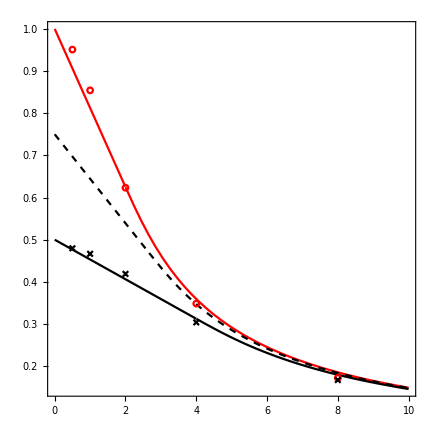

4.56304×10^8

```mathematica
aa=1.29182*10^-8;
paa=Plot[{(RPY[{x aa,0,0},aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},2aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},1.33333aa].{1,0,0})[[1]](6 π μ aa)},{x,0,10},PlotStyle->{Red,Black,{Black,Dashed}}];
pbb=ListPlot[{wetData,dampData},PlotMarkers->{{m1,ss},{m3,ss}},PlotStyle->{Red,Black}];
Show[paa,pbb,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
nvel=1/(6 π μ aa);
wetData={{0.5,4.16808522*10^8/nvel},{1,3.410819130*10^8/nvel},{2,1.87910207455024*10^8/nvel},{4,8.29870572051*10^7/nvel},{8,3.68865691791*10^7/nvel}}
dampData={{0.5,2.17998988*10^8/nvel},{1,2.0523165699549*10^8/nvel},{2,1.6736846128171*10^8/nvel},{4,9.078303775*10^7/nvel},{8,3.832321149528*10^7/nvel}}
```

{{0.5,0.913445},{1,0.747488},{2,0.411809},{4,0.181868},{8,0.0808377}}

{{0.5,0.477749},{1,0.449769},{2,0.366791},{4,0.198953},{8,0.0839861}}

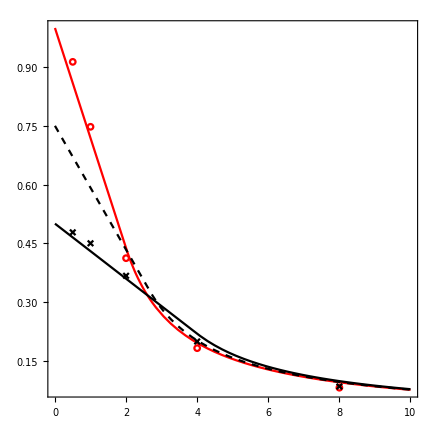

```mathematica
aa=1.29182*10^-8;
paa=Plot[{(RPY[{x aa,0,0},aa].{0,1,0})[[2]](6 π μ aa),(RPY[{x aa,0,0},2aa].{0,1,0})[[2]](6 π μ aa),(RPY[{x aa,0,0},1.33333aa].{0,1,0})[[2]](6 π μ aa)},{x,0,10},PlotStyle->{Red,Black,{Black,Dashed}}];
pbb=ListPlot[{wetData,dampData},PlotMarkers->{{m1,ss},{m3,ss}},PlotStyle->{Red,Black}];
Show[paa,pbb,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
paa=Plot[{(RPY[{x aa,0,0},aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},2aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},1.33333aa].{1,0,0})[[1]](6 π μ aa)},{x,0,10},PlotStyle->{Red,Black,{Black,Dashed}}];
pbb=ListPlot[{wetData,dampData},PlotMarkers->{{m1,ss},{m3,ss}},PlotStyle->{Red,Black}];
Show[paa,pbb,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
aa=1.62*10^-8;
RPY[{0 ,60*10^-8,0},aa].{1,0,0}
```

{6.63468×10^6,0.,0.}

```mathematica
1/(6 π μ aa)
```

3.27479×10^8

```mathematica
eps=692.96*10^-21;
dx=1.6572*10^-6/128;
Q=1.6*10^-19;
coulomb[2 dx]
```

4.38462×10^-6

```mathematica
4.3846/4.5200
```

0.970044